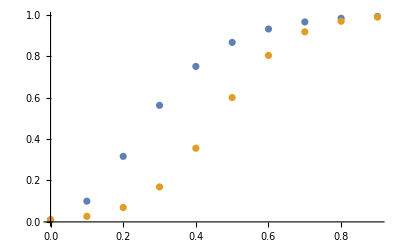

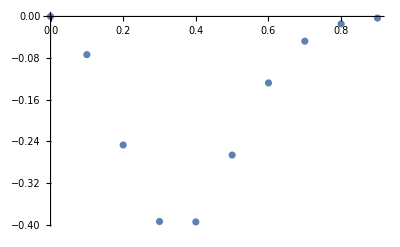

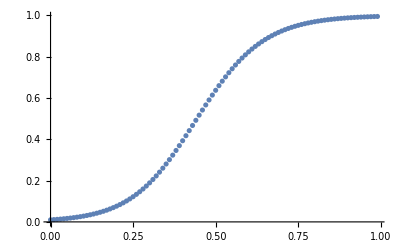

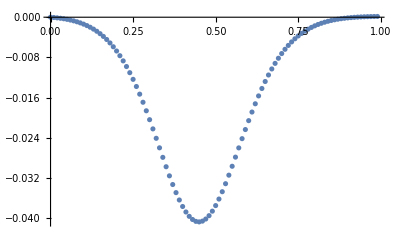

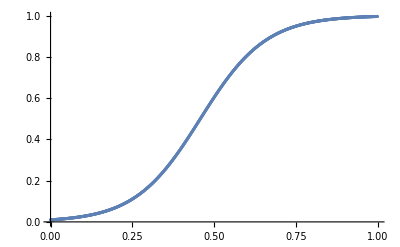

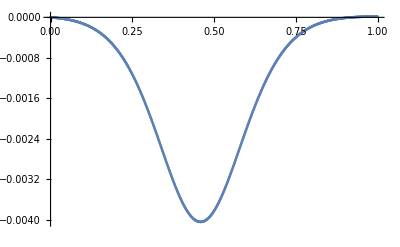

```mathematica
f[u_]=10*u*(1-u);
ur[t_]=0.01/(0.01+0.99*Exp[-10*t]);
n1=10;
n2=100;
n3=1000;
u1=Table[0,n1];
u2=Table[0,n2];
u3=Table[0,n3];
u1[[1]]=0.01;
u2[[1]]=0.01;
u3[[1]]=0.01;
h1=1/n1;
h2=1/n2;
h3=1/n3;
For[k=1,k≤n1-1,k++,
u1[[k+1]]=u/.FindRoot[u-u1[[k]]==h1*f[u],{u,u1[[k]]}];
]
For[k=1,k≤n2-1,k++,
u2[[k+1]]=u/.FindRoot[u-u2[[k]]==h2*f[u],{u,u2[[k]]}];
]
For[k=1,k≤n3-1,k++,
u3[[k+1]]=u/.FindRoot[u-u3[[k]]==h3*f[u],{u,u3[[k]]}];
]
ListPlot[Table[{(k-1)*h1,u1[[k]]},{k,1,n1}]]
(*ListPlot[{Table[{(k-1)*h1,u1[[k]]},{k,1,n1}],Table[{(k-1)*h1,ur[(k-1)*h1]},{k,1,n1}]}]*)
ListPlot[Table[{(k-1)*h1,ur[(k-1)*h1]-u1[[k]]},{k,1,n1}]]
ListPlot[Table[{(k-1)*h2,u2[[k]]},{k,1,n2}]]
ListPlot[Table[{(k-1)*h2,ur[(k-1)*h2]-u2[[k]]},{k,1,n2}]]
ListPlot[Table[{(k-1)*h3,u3[[k]]},{k,1,n3}]]
ListPlot[Table[{(k-1)*h3,ur[(k-1)*h3]-u3[[k]]},{k,1,n3}]]
```

```mathematica
u/.FindRoot[u-0.01==0.01*10*u*(1-u),{u,0.01}]
```

0.0110974

```mathematica
Newton[g_,x0_,eps_]:=
(xf=x0;
xs=xf-g[xf]/g'[xf];
While[Abs[xs-xf]>=eps,xf=xs;
xs=xf-g[xf]/g'[xf];];
xs)
gt[t_]=t^2+3*t-5;
Newton[gt,0.01,0.00000001]
FindRoot[gt[t]==0,{t,0.01}]
```

1.19258

{t→1.19258}

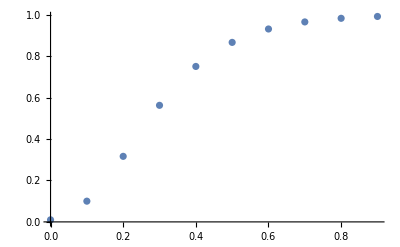

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

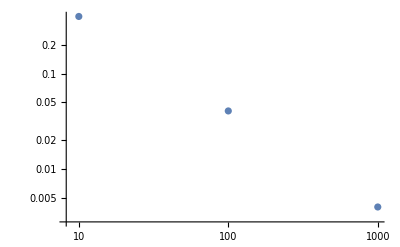

```mathematica
f[u_]=10*u*(1-u);
ur[t_]=0.01/(0.01+0.99*Exp[-10*t]);
n1=10;
n2=100;
n3=1000;
u1=Table[0,n1];
u2=Table[0,n2];
u3=Table[0,n3];
u1[[1]]=0.01;
u2[[1]]=0.01;
u3[[1]]=0.01;
h1=1/n1;
h2=1/n2;
h3=1/n3;
For[k=1,k≤n1-1,k++,
ut1[t_]=t-u1[[k]]-h1*f[t];
u1[[k+1]]=Newton[ut1,u1[[k]],0.00001];
]
For[k=1,k≤n2-1,k++,
ut2[t_]=t-u2[[k]]-h2*f[t];
u2[[k+1]]=Newton[ut2,u2[[k]],0.00001];
]
For[k=1,k≤n3-1,k++,
ut3[t_]=t-u3[[k]]-h3*f[t];
u3[[k+1]]=Newton[ut3,u3[[k]],0.00001];
]
ListPlot[Table[{(k-1)*h1,u1[[k]]},{k,1,n1}]]
ListPlot[Table[{(k-1)*h1,ur[(k-1)*h1]-u1[[k]]},{k,1,n1}]]
ListPlot[Table[{(k-1)*h2,u2[[k]]},{k,1,n2}]]
ListPlot[Table[{(k-1)*h2,ur[(k-1)*h2]-u2[[k]]},{k,1,n2}]]
ListPlot[Table[{(k-1)*h3,u3[[k]]},{k,1,n3}]]
ListPlot[Table[{(k-1)*h3,ur[(k-1)*h3]-u3[[k]]},{k,1,n3}]]


errTable1=Table[0,n1];
For[k=1,k<=n1,k++,
errTable1[[k]]=Abs[ur[(k-1)*h1]-u1[[k]]];
]
errTable2=Table[0,n2];
For[k=1,k<=n2,k++,
errTable2[[k]]=Abs[ur[(k-1)*h2]-u2[[k]]];
]
errTable3=Table[0,n3];
For[k=1,k<=n3,k++,
errTable3[[k]]=Abs[ur[(k-1)*h3]-u3[[k]]];
]
narr=List[n1,n2,n3];
errarr=List[Max[errTable1],Max[errTable2],Max[errTable3]];
ListLogLogPlot[Table[{narr[[k]],errarr[[k]]},{k,1,3}]]
```

```mathematica
f[u_]=10*u*(1-u);
ur[t_]=0.01/(0.01+0.99*Exp[-10*t]);
b=6;
h1=0.5;
h2=0.25;
h3=0.15;
h4=0.01;
n1=b/h1;
n2=b/h2;
n3=b/h3;
n4=b/h4;
u1=Table[0,n1];
u2=Table[0,n2];
u3=Table[0,n3];
u4=Table[0,n4];
u1[[1]]=0.01;
u2[[1]]=0.01;
u3[[1]]=0.01;
u4[[1]]=0.01;
For[k=1,k≤n1-1,k++,
(*u1[[k+1]]=Newton[ut1,u1[[k]]+h1*f[u1[[k]]],0.00001];*)
u1[[k+1]]=u/.FindRoot[u-u1[[k]]-h1*f[u]==0,{u,u1[[k]]+h1*f[u1[[k]]]}];
]
For[k=1,k≤n2-1,k++,
(*u2[[k+1]]=Newton[ut2,u2[[k]]+h2*f[u2[[k]]],0.00001];*)
u2[[k+1]]=u/.FindRoot[u-u2[[k]]-h2*f[u]==0,{u,u2[[k]]+h2*f[u2[[k]]]}];
]
For[k=1,k≤n3-1,k++,
(*u3[[k+1]]=Newton[ut3,u3[[k]]+h3*f[u3[[k]]],0.00001];*)
u3[[k+1]]=u/.FindRoot[u-u3[[k]]-h3*f[u]==0,{u,u3[[k]]+h3*f[u3[[k]]]}];
]
For[k=1,k≤n4-1,k++,
(*u4[[k+1]]=Newton[ut4,u4[[k]]+h4*f[u4[[k]]],0.00001];*)
u4[[k+1]]=u/.FindRoot[u-u4[[k]]-h4*f[u]==0,{u,u4[[k]]+h4*f[u4[[k]]]}];
]


uu1=Table[0,n1];
uu2=Table[0,n2];
uu3=Table[0,n3];
uu4=Table[0,n4];
uu1[[1]]=0.01;
uu2[[1]]=0.01;
uu3[[1]]=0.01;
uu4[[1]]=0.01;
For[k=1,k≤n1-1,k++,
uu1[[k+1]]=uu1[[k]]+h1*f[uu1[[k]]];
]
For[k=1,k≤n2-1,k++,
uu2[[k+1]]=uu2[[k]]+h2*f[uu2[[k]]];
]
For[k=1,k≤n3-1,k++,
uu3[[k+1]]=uu3[[k]]+h3*f[uu3[[k]]];
]
For[k=1,k≤n4-1,k++,
uu4[[k+1]]=uu4[[k]]+h4*f[uu4[[k]]];
]
ListLinePlot[{Table[{(k-1)*h1,u1[[k]]},{k,1,n1}],Table[{(k-1)*h1,uu1[[k]]},{k,1,n1}]},PlotLabels->{"IMPL","EXPL"},PlotRange->All]
ListLinePlot[{Table[{(k-1)*h2,u2[[k]]},{k,1,n2}],Table[{(k-1)*h2,uu2[[k]]},{k,1,n2}]},PlotLabels->{"IMPL","EXPL"},PlotRange->All]
ListLinePlot[{Table[{(k-1)*h3,u3[[k]]},{k,1,n3}],Table[{(k-1)*h3,uu3[[k]]},{k,1,n3}]},PlotLabels->{"IMPL","EXPL"},PlotRange->All]
ListLinePlot[{Table[{(k-1)*h4,u4[[k]]},{k,1,n4}],Table[{(k-1)*h4,uu4[[k]]},{k,1,n4}]},PlotLabels->{"IMPL","EXPL"},PlotRange->All]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

-Graphics-

-Graphics-

-Graphics-